## Model Output Generation for Basis Expansion Unit Tests

The hope is that by typing it here in Mathematica with pretty-print, I will duplicate the equations correctly. Then I can use the output from these equations as model outputs for the unit tests that construct the H matrix.

```mathematica
L=10.;
b=1/6.;
a=1.;
V0=100;
nb=10;
```

```mathematica
Fnm[n_,m_,x_]:=If[n==m,x/L-Sin[2 π n x/L]/(2π n),Sin[(m-n)π x/L]/(π(m-n))-Sin[(m+n)π x/L]/(π(m+n))];
```

```mathematica
hnm[n_,m_,s_,b_]:=Fnm[n,m,s+b/2]-Fnm[n,m,s-b/2];
xr[x_,r_]:=-a/2+r a;
```

```mathematica
TFnm[x_]:=Table[{n,m,x,Fnm[n,m,x]},{n,10},{m,10}]//Flatten//Partition[#,4]&;
```

```mathematica
Export["/Users/trunks/codes/782/tests/model/Fnm.08.dat",TFnm[0.8],"Table"]
```

/Users/trunks/codes/782/tests/model/Fnm.08.dat

```mathematica
Thnm[x_,r_]:=Table[{n,m,r, x,hnm[n,m,xr[x,r],b]},{n,10},{m,10}]//Flatten//Partition[#,5]&;
```

```mathematica
xs={0.1,0.3,0.5,0.8};
rs={1,3,5,9};
```

```mathematica
Do[fname=StringForm["/Users/trunks/codes/782/tests/model/hnm.``_``.dat",xi,ri]//ToString;
Export[fname,Thnm[xs⟦xi⟧,rs⟦ri⟧]];,
{xi,Length[xs]},{ri,Length[rs]}]
```

```mathematica
En0[n_]:=n^2 π^2/L^2;
```

```mathematica
Export["/Users/trunks/codes/782/tests/model/En0.dat",Table[En0[n],{n,100}],"Table"]
```

/Users/trunks/codes/782/tests/model/En0.dat

```mathematica
H=Table[If[n==m,En0[n],0]+V0 Sum[hnm[n,m,xr[0,r],b],{r,nb}],{n,100},{m,100}];
```

```mathematica
Export["/Users/trunks/codes/782/tests/model/H.dat",H,"Table"]
```

/Users/trunks/codes/782/tests/model/H.dat

### Analytic K-P Solution

```mathematica
V0=10^2;
a=1;
b=1/6;
L=10.;
```

```mathematica
bands=Table[Table[{n/(3L),(en/.FindRoot[Cos[n/L a]==Cos[Sqrt[en]a]+(V0 b)/(2Sqrt[en])Sin[Sqrt[en]a],{en,en0 π^2}]⟦1⟧)/π^2},{en0,{1,3,7}}],{n,0,30,0.25}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{{0.,0.657862},{0.,4.},{0.,6.33392}},{{0.00833333,0.657902},{0.00833333,3.9997},{0.00833333,6.33434}},{{0.0166667,0.658024},{0.0166667,3.9988},{0.0166667,6.3356}},{{0.025,0.658226},{0.025,3.9973},{0.025,6.33771}},{{0.0333333,0.658509},{0.0333333,3.99522},{0.0333333,6.34065}},{{0.0416667,0.658873},{0.0416667,3.99254},{0.0416667,6.34442}},{{0.05,0.659317},{0.05,3.98928},{0.05,6.34902}},{{0.0583333,0.659842},{0.0583333,3.98544},{0.0583333,6.35444}},{{0.0666667,0.660448},{0.0666667,3.98104},{0.0666667,6.36067}},{{0.075,0.661134},{0.075,3.97608},{0.075,6.3677}},{{0.0833333,0.6619},{0.0833333,3.97057},{0.0833333,6.37552}},{{0.0916667,0.662745},{0.0916667,3.96454},{0.0916667,6.38411}},{{0.1,0.663671},{0.1,3.95798},{0.1,6.39347}},{{0.108333,0.664676},{0.108333,3.95091},{0.108333,6.40358}},{{0.116667,0.66576},{0.116667,3.94334},{0.116667,6.41443}},{{0.125,0.666924},{0.125,3.9353},{0.125,6.42599}},{{0.133333,0.668166},{0.133333,3.9268},{0.133333,6.43827}},{{0.141667,0.669486},{0.141667,3.91784},{0.141667,6.45123}},{{0.15,0.670884},{0.15,3.90846},{0.15,6.46488}},{{0.158333,0.672361},{0.158333,3.89866},{0.158333,6.47917}},{{0.166667,0.673914},{0.166667,3.88845},{0.166667,6.49412}},{{0.175,0.675544},{0.175,3.87787},{0.175,6.50968}},{{0.183333,0.677251},{0.183333,3.86692},{0.183333,6.52586}},{{0.191667,0.679034},{0.191667,3.85561},{0.191667,6.54262}},{{0.2,0.680892},{0.2,3.84397},{0.2,6.55997}},{{0.208333,0.682825},{0.208333,3.83202},{0.208333,6.57787}},{{0.216667,0.684833},{0.216667,3.81976},{0.216667,6.59631}},{{0.225,0.686915},{0.225,3.80721},{0.225,6.61528}},{{0.233333,0.68907},{0.233333,3.7944},{0.233333,6.63477}},{{0.241667,0.691298},{0.241667,3.78133},{0.241667,6.65474}},{{0.25,0.693599},{0.25,3.76801},{0.25,6.6752}},{{0.258333,0.695971},{0.258333,3.75447},{0.258333,6.69613}},{{0.266667,0.698413},{0.266667,3.74072},{0.266667,6.7175}},{{0.275,0.700926},{0.275,3.72678},{0.275,6.73931}},{{0.283333,0.703508},{0.283333,3.71264},{0.283333,6.76154}},{{0.291667,0.706159},{0.291667,3.69834},{0.291667,6.78418}},{{0.3,0.708877},{0.3,3.68388},{0.3,6.80722}},{{0.308333,0.711663},{0.308333,3.66927},{0.308333,6.83064}},{{0.316667,0.714515},{0.316667,3.65453},{0.316667,6.85442}},{{0.325,0.717432},{0.325,3.63966},{0.325,6.87857}},{{0.333333,0.720413},{0.333333,3.62469},{0.333333,6.90306}},{{0.341667,0.723457},{0.341667,3.60962},{0.341667,6.92788}},{{0.35,0.726564},{0.35,3.59446},{0.35,6.95303}},{{0.358333,0.729732},{0.358333,3.57922},{0.358333,6.97849}},{{0.366667,0.732961},{0.366667,3.56391},{0.366667,7.00424}},{{0.375,0.736248},{0.375,3.54854},{0.375,7.03029}},{{0.383333,0.739594},{0.383333,3.53312},{0.383333,7.05661}},{{0.391667,0.742996},{0.391667,3.51767},{0.391667,7.08321}},{{0.4,0.746454},{0.4,3.50218},{0.4,7.11006}},{{0.408333,0.749966},{0.408333,3.48668},{0.408333,7.13716}},{{0.416667,0.753531},{0.416667,3.47115},{0.416667,7.16451}},{{0.425,0.757148},{0.425,3.45563},{0.425,7.19208}},{{0.433333,0.760814},{0.433333,3.4401},{0.433333,7.21987}},{{0.441667,0.76453},{0.441667,3.42459},{0.441667,7.24788}},{{0.45,0.768293},{0.45,3.40909},{0.45,7.27609}},{{0.458333,0.772101},{0.458333,3.39362},{0.458333,7.30449}},{{0.466667,0.775954},{0.466667,3.37818},{0.466667,7.33308}},{{0.475,0.779849},{0.475,3.36278},{0.475,7.36185}},{{0.483333,0.783785},{0.483333,3.34743},{0.483333,7.39078}},{{0.491667,0.787759},{0.491667,3.33213},{0.491667,7.41988}},{{0.5,0.791771},{0.5,3.31688},{0.5,7.44913}},{{0.508333,0.795819},{0.508333,3.30171},{0.508333,7.47851}},{{0.516667,0.799899},{0.516667,3.2866},{0.516667,7.50804}},{{0.525,0.804012},{0.525,3.27157},{0.525,7.53769}},{{0.533333,0.808153},{0.533333,3.25663},{0.533333,7.56745}},{{0.541667,0.812322},{0.541667,3.24178},{0.541667,7.59732}},{{0.55,0.816516},{0.55,3.22702},{0.55,7.6273}},{{0.558333,0.820734},{0.558333,3.21236},{0.558333,7.65736}},{{0.566667,0.824971},{0.566667,3.19782},{0.566667,7.68751}},{{0.575,0.829228},{0.575,3.18338},{0.575,7.71772}},{{0.583333,0.8335},{0.583333,3.16906},{0.583333,7.748}},{{0.591667,0.837785},{0.591667,3.15487},{0.591667,7.77833}},{{0.6,0.842082},{0.6,3.1408},{0.6,7.80871}},{{0.608333,0.846387},{0.608333,3.12687},{0.608333,7.83912}},{{0.616667,0.850697},{0.616667,3.11308},{0.616667,7.86955}},{{0.625,0.855011},{0.625,3.09943},{0.625,7.89999}},{{0.633333,0.859324},{0.633333,3.08593},{0.633333,7.93043}},{{0.641667,0.863635},{0.641667,3.07259},{0.641667,7.96086}},{{0.65,0.86794},{0.65,3.05941},{0.65,7.99127}},{{0.658333,0.872237},{0.658333,3.04639},{0.658333,8.02165}},{{0.666667,0.876521},{0.666667,3.03355},{0.666667,8.05198}},{{0.675,0.880791},{0.675,3.02088},{0.675,8.08225}},{{0.683333,0.885043},{0.683333,3.00839},{0.683333,8.11244}},{{0.691667,0.889273},{0.691667,2.99608},{0.691667,8.14254}},{{0.7,0.893479},{0.7,2.98397},{0.7,8.17254}},{{0.708333,0.897656},{0.708333,2.97206},{0.708333,8.20242}},{{0.716667,0.901802},{0.716667,2.96034},{0.716667,8.23217}},{{0.725,0.905913},{0.725,2.94884},{0.725,8.26176}},{{0.733333,0.909985},{0.733333,2.93754},{0.733333,8.29118}},{{0.741667,0.914014},{0.741667,2.92646},{0.741667,8.32041}},{{0.75,0.917998},{0.75,2.9156},{0.75,8.34943}},{{0.758333,0.921932},{0.758333,2.90497},{0.758333,8.37822}},{{0.766667,0.925813},{0.766667,2.89457},{0.766667,8.40676}},{{0.775,0.929637},{0.775,2.8844},{0.775,8.43502}},{{0.783333,0.933399},{0.783333,2.87448},{0.783333,8.46298}},{{0.791667,0.937097},{0.791667,2.8648},{0.791667,8.49062}},{{0.8,0.940726},{0.8,2.85538},{0.8,8.51791}},{{0.808333,0.944282},{0.808333,2.84621},{0.808333,8.54483}},{{0.816667,0.947762},{0.816667,2.8373},{0.816667,8.57134}},{{0.825,0.951162},{0.825,2.82866},{0.825,8.59741}},{{0.833333,0.954477},{0.833333,2.82028},{0.833333,8.62301}},{{0.841667,0.957704},{0.841667,2.81219},{0.841667,8.64811}},{{0.85,0.960839},{0.85,2.80437},{0.85,8.67268}},{{0.858333,0.963878},{0.858333,2.79683},{0.858333,8.69668}},{{0.866667,0.966818},{0.866667,2.78959},{0.866667,8.72007}},{{0.875,0.969655},{0.875,2.78264},{0.875,8.74282}},{{0.883333,0.972385},{0.883333,2.77598},{0.883333,8.76488}},{{0.891667,0.975005},{0.891667,2.76963},{0.891667,8.78622}},{{0.9,0.977511},{0.9,2.76358},{0.9,8.80679}},{{0.908333,0.979899},{0.908333,2.75784},{0.908333,8.82655}},{{0.916667,0.982167},{0.916667,2.75242},{0.916667,8.84547}},{{0.925,0.984312},{0.925,2.74731},{0.925,8.86349}},{{0.933333,0.98633},{0.933333,2.74252},{0.933333,8.88057}},{{0.941667,0.988218},{0.941667,2.73805},{0.941667,8.89668}},{{0.95,0.989974},{0.95,2.73391},{0.95,8.91176}},{{0.958333,0.991596},{0.958333,2.7301},{0.958333,8.92578}},{{0.966667,0.99308},{0.966667,2.72663},{0.966667,8.93869}},{{0.975,0.994425},{0.975,2.72348},{0.975,8.95046}},{{0.983333,0.995629},{0.983333,2.72068},{0.983333,8.96105}},{{0.991667,0.996689},{0.991667,2.71821},{0.991667,8.97043}},{{1.,0.997604},{1.,2.71609},{1.,8.97856}}}

```mathematica
bands⟦All,1⟧
```

```mathematica
Export["/Users/trunks/codes/782/analytic/KP.bands.1",band1,"TSV"]
Export["/Users/trunks/codes/782/analytic/KP.bands.2",band2,"TSV"]
Export["/Users/trunks/codes/782/analytic/KP.bands.3",band3,"TSV"]
```

/Users/trunks/codes/782/analytic/KP.bands.1

/Users/trunks/codes/782/analytic/KP.bands.2

/Users/trunks/codes/782/analytic/KP.bands.3

```mathematica
band1=bands⟦All,1⟧;
band2={Abs[1.-#⟦1⟧]+1., #⟦2⟧}&/@Reverse[bands⟦All,2⟧];
band3={#⟦1⟧+2., #⟦2⟧}&/@bands⟦All,3⟧;
```

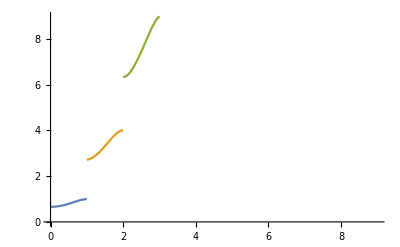

```mathematica
ListPlot[{band1,band2,band3},Joined->True,PlotRange->{{0,9},Automatic}]
```

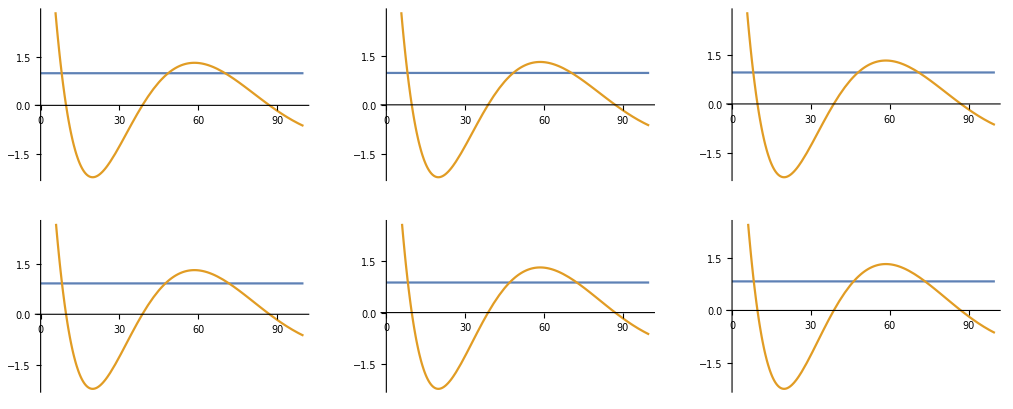

```mathematica
Table[Plot[{Cos[n/L a],(Cos[Sqrt[en]a]+V0/(Sqrt[en]a)Sin[Sqrt[en]a])/π^2},{en,0,100}],{n,1,6}]//Partition[#,3]&//GraphicsGrid
```

```mathematica
(en/.FindRoot[Cos[2/L a]==Cos[Sqrt[en]a]+(2V0)/Sqrt[en] Sin[Sqrt[en]a],{en,2.9}]⟦1⟧)
```

9.67706

```mathematica
3.03/π^2
```

0.307003